```mathematica
Manipulate[Show[

ParametricPlot[{Cos[t],Sin[t]},{t,0,2Pi},PlotStyle->Brown],
ParametricPlot[{(Cos[c]-Cos[a])*r +Cos[a],(Sin[c]-Sin[a])*r+Sin[a]},{r,0,1},PlotStyle->Purple],
ParametricPlot[{(Cos[b]-Cos[a])*r +Cos[a],(Sin[b]-Sin[a])*r+Sin[a]},{r,0,1},PlotStyle->Orange],
ParametricPlot[{(Cos[c]-Cos[b])*r +Cos[b],(Sin[c]-Sin[b])*r+Sin[b]},{r,0,1},PlotStyle->Green],

Graphics[{Red,PointSize[.05],Point[{Cos[a],Sin[a]}]}],
Graphics[{Yellow,PointSize[.05],Point[{Cos[b],Sin[b]}]}],
Graphics[{Blue,PointSize[.05],Point[{Cos[c],Sin[c]}]}],
Graphics[{Purple,PointSize[.05],Point[{Cos[b+Pi],Sin[b+Pi]}]}],
Graphics[{Green,PointSize[.05],Point[{Cos[a+Pi],Sin[a+Pi]}]}],
Graphics[{Orange,PointSize[.05],Point[{Cos[c+Pi],Sin[c+Pi]}]}]],
{{a,0,"Red Point"},0,2Pi,Appearance->"Labeled"},
{{b,0,"Yellow Point"},0,2Pi,Appearance->"Labeled"},
{{c,0,"Blue Point"},0,2Pi,Appearance->"Labeled"}
]
```

```mathematica
Show[Plot3D[Piecewise[
{{(y-x)/(2Pi),y>x&& y < x+ Pi},
{(x-y)/(2Pi),y<x && y > x-Pi},
{1-(y-x)/(2Pi),y>x+Pi},
{1-(x-y)/(2Pi),y>y-Pi}
}


],{y,0,2Pi},{x,0,2Pi},PlotRange->{{0,2Pi},{0,2Pi},{0,1}}]]
```

-Graphics3D-

```mathematica
Integrate[(y-x)/(2Pi),{x,0,Pi},{y,x,x+Pi}]+Integrate[(y-x)/(2Pi),{x,Pi,2Pi},{y,x,2Pi}]

Integrate[(x-y)/(2Pi),{x,0,Pi},{y,0,x}]+Integrate[(x-y)/(2Pi),{x,Pi,2Pi},{y,x-Pi,x}]

Integrate[1-(y-x)/(2Pi),{x,0,Pi},{y,x+Pi,2Pi}]

Integrate[1-(x-y)/(2Pi),{x,Pi,2Pi},{y,0,x-Pi}]
```

π^2/3

π^2/3

π^2/6

π^2/6

```mathematica
(Pi^2/3+Pi^2/3+Pi^2/6+Pi^2/6)/(4Pi^2)
```

1/4

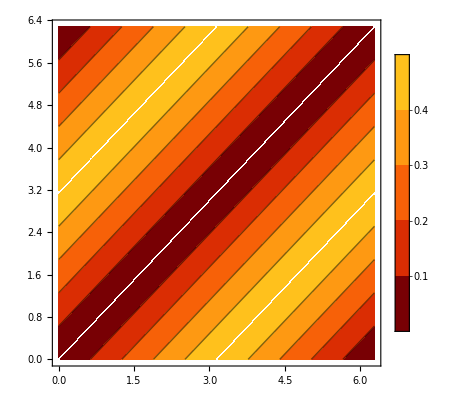

```mathematica
ContourPlot[Piecewise[
{{(y-x)/(2Pi),y>=x&& y < x+ Pi},
{(x-y)/(2Pi),y<=x && y > x-Pi},
{1-(y-x)/(2Pi),y>x+Pi},
{1-(x-y)/(2Pi),y>y-Pi}
}


],{x,0,2Pi},{y,0,2Pi},ColorFunction->ColorData["SolarColors"],PlotLegends->Automatic]
```

```mathematica
Integrate[(y-x)/(2Pi),{x,0,Pi},{y,x,x+Pi}]+Integrate[(y-x)/(2Pi),{x,Pi,2Pi},{y,x,2Pi}]+Integrate[1-(y-x)/(2Pi),{x,0,Pi},{y,x+Pi,2Pi}]
```

π^2/2